{{S→InterpolatingFunction[…],M→InterpolatingFunction[…]}}

{{SS→InterpolatingFunction[…],MM→InterpolatingFunction[…]}}

{{SSS→InterpolatingFunction[…],MMM→InterpolatingFunction[…]}}

{{SSSS→InterpolatingFunction[…],MMMM→InterpolatingFunction[…]}}

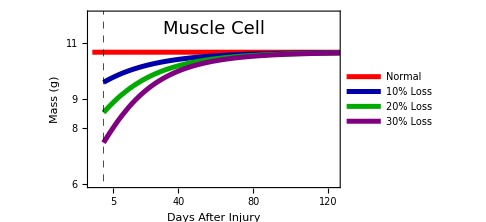

-Graphics-(B)

```mathematica
P0=0.479;P1=0.133;v0=0.087;v1=5.591;d=0.05;m=1000;
s1=NDSolve[{S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))* (v0+v1/(1+M[x]/m))* S[x]-d*M[x],S[0]==112.6,M[0]==2139.4},{S,M},{x,0,700}]
s2=NDSolve[{SS'[x]==(2 *(P0+P1/(1+MM[x]/m))-1)* (v0+v1/(1+MM[x]/m))*SS[x],MM'[x]==2 *(1-P0-P1/(1+MM[x]/m))* (v0+v1/(1+MM[x]/m))* SS[x]-d*MM[x],SS[376]==0.9*274.974,MM[376]==0.9*5333.33},{SS,MM},{x,376,1000}]
s3=NDSolve[{SSS'[x]==(2 *(P0+P1/(1+MMM[x]/m))-1)* (v0+v1/(1+MMM[x]/m))*SSS[x],MMM'[x]==2 *(1-P0-P1/(1+MMM[x]/m))* (v0+v1/(1+MMM[x]/m))* SSS[x]-d*MMM[x],SSS[376]==0.8*274.974,MMM[376]==0.8*5333.33},{SSS,MMM},{x,376,700}]
s4=NDSolve[{SSSS'[x]==(2 *(P0+P1/(1+MMMM[x]/m))-1)* (v0+v1/(1+MMMM[x]/m))*SSSS[x],MMMM'[x]==2 *(1-P0-P1/(1+MMMM[x]/m))* (v0+v1/(1+MMMM[x]/m))* SSSS[x]-d*MMMM[x],SSSS[376]==0.7*274.974,MMMM[376]==0.7*5333.33},{SSSS,MMMM},{x,376,700}]
p1=Plot[(0.002*M[x]/.s1),{x,370,700},PlotLegends->Placed[LineLegend[{"Normal"},LabelStyle->{FontSize->16,FontFamily->"Times New Roman"}],{0.78,0.6}],PlotRange->{{370,500},{6,12}},PlotStyle->{Red,Thickness[0.01]},GridLines->{{376},{}},GridLinesStyle->Directive[Black,Dashed](*,Ticks->{{{380,"4"},{385,""},{400,"24"},{420,"44"},{440,"64"},{460,"84"},{480,"104"},{500,"124"}},{6,7,8,9,10,11,12}}*),Epilog->Text[Style["Muscle Cell",Black,(*Bold,Italic*)18,FontFamily->"Times New Roman"],Scaled[{.5,.9}]]];
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
p2=Plot[(0.002*MM[x]/.s2),{x,376,700},PlotLegends->Placed[LineLegend[{"10% Loss"},LabelStyle->{FontSize->16,FontFamily->"Times New Roman"}],{0.8,0.5}],PlotRange->{{376,600},{0,20}},PlotStyle->{Darker[Blue],Thickness[0.01]}];

p3=Plot[(0.002*MMM[x]/.s3),{x,376,700},PlotLegends->Placed[LineLegend[{"20% Loss"},LabelStyle->{FontSize->16,FontFamily->"Times New Roman"}],{0.8,0.4}],PlotRange->{{376,600},{0,20}},PlotStyle->{Darker[Green],Thickness[0.01]}];

p4=Plot[(0.002*MMMM[x]/.s4),{x,376,700},PlotLegends->Placed[LineLegend[{"30% Loss"},LabelStyle->{FontSize->16,FontFamily->"Times New Roman"}],{0.8,0.3}],PlotRange->{{376,600},{0,20}},PlotStyle->{Purple,Thickness[0.01]}];

(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
pl2s=Show[p1,p2,p3,p4,ImageSize->Medium,Frame->True,(*FrameLabel->{"Days after injury","Growth Ratio"},*)FrameLabel->{Style["Days After Injury",18(*,Bold*)],Style["Mass (g)",18(*,Bold*)]}(*FrameStyle->Directive[Black,12]*)(*ImageSize->400*),(*PlotLabel->"Muscle Cell",*)LabelStyle->Directive[(*Bold,*)Black,18,FontFamily->"Times New Roman"],FrameTicks->{{{381,"5"},{386,""},{391,""},{396,"20"},{401,""},{406,""},{411,""},{416,"40"},{421,""},{426,""},{431,""},{436,"60"},{441,""},{446,""},{451,""},{456,"80"},{461,""},{466,""},{471,""},{476,"100"},{481,""},{486,""},{491,""},{496,"120"},{500,""}},(*{6,7,8,9,10,11,12}*){{6,"6"},{6.25,""},{6.5,""},{6.75,""},{7,"7"},{7.25,""},{7.5,""},{7.75,""},{8,"8"},{8.25,""},{8.5,""},{8.75,""},{9,"9"},{8.25,""},{8.5,""},{8.75,""},{9,"9"},{9.25,""},{9.5,""},{9.75,""},{10,"10"},{10.25,""},{10.5,""},{10.75,""},{11,"11"},{11.25,""},{11.5,""},{11.75,""},{12,"12"}},Automatic,Automatic},FrameTicksStyle->Directive[Black,14]]
pl22=Labeled[pl2s,Style["(B)","Section",Black],{{Top,Left}}]
```